```mathematica
? Fouri*
```

RowBox[{"FourierCoefficient", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["t", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives the StyleBox["n", "TI"]SuperscriptBox["", "th"] coefficient in the Fourier series expansion of StyleBox["expr", "TI"].
RowBox[{"FourierCoefficient", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["t", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["t", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives a multidimensional Fourier coefficient.

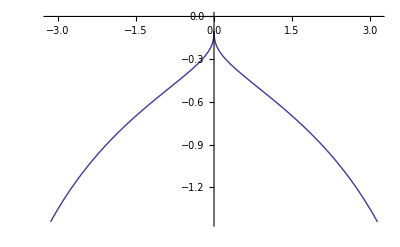

```mathematica
Plot[1/Log[Abs[x/(2π)]],{x,-π,π}]
```

{-1.51468,0.463807,-0.0420307,0.0721453,-0.00749555,0.0293791,-0.00169937,0.0163544,-0.0000674108,0.0106247,0.000497556,0.00756464,0.000703628,0.00572143,0.000769241,0.00451626,0.000775118,0.00367995,0.000754815,0.00307283,0.000723419}

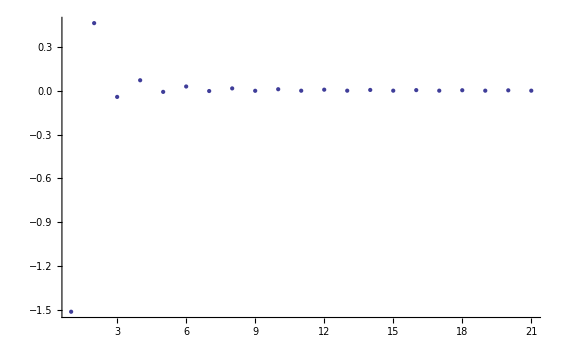

```mathematica
f[x_]:=1/Log[Abs[x/(2π)]]
list=Table[NIntegrate[(f[x] Cos[n x])/π,{x,-π,π}],{n,0,20}]
ListPlot[list]
```

```mathematica
∫_-π^π Cos[x]^2 ⅆx
```

π